# B->X_s γ

Based on [CMM:1996A]. See Eqs. (39)-(40), p. 9 therein. We fit a polynomial in z, Log[z], δ and Log[1 -δ ]
to the loop functions f_22 and f_27. The relative error between our approximations and the loop functions
is smaller than 10^-9 for f_22 and 10^-6 for f_27 for  z ∈ [0.03, 0.12]  and δ ∈ [1/36, 1/3].

## Basics

Basic Loop Function

```mathematica
G1 = -2 ArcTan[Sqrt[t / (4 - t)]]^2;
G2= -Pi^2/2 + 2Log[(Sqrt[t] + Sqrt[t - 4]) / 2]^2 - I 2 Pi Log[(Sqrt[t] + Sqrt[t - 4])/2];
G[t_] := Piecewise[{{G1, t < 4}}, G2]
```

Evaluation

```mathematica
evaluationPoints = Flatten[Outer[List, Range[3/100, 12/100, 5/1000], Range[1/36, 1/3, 1/36]], 1];
Length[evaluationPoints]
```

228

```mathematica
ccName[i_, j_, k_, l_] := ToExpression["cc"<> ToString[i] <>ToString[j] <> ToString[k]<> ToString[l]] 
polynomial = (Flatten[Table[ccName[i, j, k, l] (1-z)^i Log[z]^j (1- delta)^k Log[1 - delta]^l, {i, 0,4}, {j, 0, i}, {k, 0, 4}, {l, 0, k}]] /. {List -> Plus});
coefficients = Flatten[Table[ccName[i, j, k, l], {i, 0, 4}, {j, 0, i}, {k, 0, 4}, {l, 0, k}]];
Length[coefficients]
```

225

f_22

### I1

```mathematica
f22I1Function[z_, delta_] := NIntegrate[(1 - z * t) Abs[G[t] / t + 1/2]^2, {t, 0, (1 - delta)/z}]
f22I1Data =Re[Flatten[{#, Apply[f22I1Function, #]}] &/@ evaluationPoints];
```

```mathematica
f22I1Model = NonlinearModelFit[f22I1Data, polynomial,coefficients, {z, delta}] ;
f22I1Model["BestFitParameters"]
f22I1 = f22I1Model["Function"];
Max[f22I1Model["FitResiduals"]]
Max[f22I1Model["StandardizedResiduals"]]
```

{cc0000→14.0986,cc0010→18.3053,cc0011→-37.0877,cc0020→23.6929,cc0021→-60.74,cc0022→47.9655,cc0030→29.1327,cc0031→-93.5889,cc0032→133.35,cc0033→72.8166,cc0040→33.9896,cc0041→-140.33,cc0042→182.615,cc0043→6.02275,cc0044→-1036.94,cc1000→-80.8631,cc1010→-108.43,cc1011→209.276,cc1020→-138.638,cc1021→344.801,cc1022→-277.427,cc1030→-168.919,cc1031→546.519,cc1032→-612.144,cc1033→-341.315,cc1040→-198.289,cc1041→820.673,cc1042→-1222.7,cc1043→143.42,cc1044→5580.26,cc1100→69.5085,cc1110→93.7854,cc1111→-172.85,cc1120→120.314,cc1121→-287.604,cc1122→245.695,cc1130→147.225,cc1131→-455.532,cc1132→509.942,cc1133→97.6227,cc1140→173.303,cc1141→-687.604,cc1142→944.647,cc1143→-291.319,cc1144→-2861.55,cc2000→255.116,cc2010→346.384,cc2011→-645.194,cc2020→443.458,cc2021→-1085.74,cc2022→919.368,cc2030→541.49,cc2031→-1719.75,cc2032→1945.42,cc2033→838.473,cc2040→635.986,cc2041→-2590.82,cc2042→3687.38,cc2043→-761.108,cc2044→-14545.1,cc2100→62.2356,cc2110→84.0348,cc2111→-154.825,cc2120→107.752,cc2121→-258.547,cc2122→222.46,cc2130→131.792,cc2131→-409.209,cc2132→461.25,cc2133→102.797,cc2140→155.137,cc2141→-617.827,cc2142→851.24,cc2143→-245.523,cc2144→-2712.5,cc2200→-0.247386,cc2210→-0.289568,cc2211→1.07215,cc2220→-0.305835,cc2221→2.87756,cc2222→0.664874,cc2230→-0.287484,cc2231→4.56945,cc2232→-8.02926,cc2233→-43.4498,cc2240→-0.206185,cc2241→6.46468,cc2242→-15.5412,cc2243→-14.7157,cc2244→301.302,cc3000→-116.718,cc3010→-157.105,cc3011→297.27,cc3020→-201.016,cc3021→496.366,cc3022→-405.046,cc3030→-245.186,cc3031→787.015,cc3032→-896.693,cc3033→-478.374,cc3040→-287.835,cc3041→1184.24,cc3042→-1704.99,cc3043→306.263,cc3044→7296.49,cc3100→6.84452,cc3110→9.1925,cc3111→-15.1921,cc3120→11.8543,cc3121→-26.4361,cc3122→29.046,cc3130→14.6241,cc3131→-41.4662,cc3132→50.1131,cc3133→-33.1307,cc3140→17.2636,cc3141→-62.762,cc3142→71.0895,cc3143→-38.9331,cc3144→31.442,cc3200→16.6629,cc3210→22.6193,cc3211→-42.0964,cc3220→28.9903,cc3221→-69.6476,cc3222→59.886,cc3230→35.4668,cc3231→-110.391,cc3232→122.097,cc3233→27.5649,cc3240→41.7346,cc3241→-166.597,cc3242→234.124,cc3243→-60.7358,cc3244→-775.669,cc3300→3.11708,cc3310→4.23161,cc3311→-8.09994,cc3320→5.40136,cc3321→-13.6917,cc3322→11.237,cc3330→6.57722,cc3331→-21.6952,cc3332→24.4382,cc3333→18.0116,cc3340→7.69467,cc3341→-32.5893,cc3342→48.9786,cc3343→-3.22689,cc3344→-250.549,cc4000→175.533,cc4010→237.263,cc4011→-439.483,cc4020→304.162,cc4021→-726.046,cc4022→611.515,cc4030→372.346,cc4031→-1151.38,cc4032→1273.61,cc4033→211.323,cc4040→438.302,cc4041→-1738.49,cc4042→2406.62,cc4043→-739.36,cc4044→-7219.48,cc4100→-7.06158,cc4110→-9.47598,cc4111→20.8498,cc4120→-12.0091,cc4121→32.8335,cc4122→-18.4786,cc4130→-14.4728,cc4131→52.5622,cc4132→-56.8575,cc4133→-106.092,cc4140→-16.7947,cc4141→78.4151,cc4142→-140.243,cc4143→-7.52708,cc4144→996.276,cc4200→12.1568,cc4210→16.6087,cc4211→-30.2281,cc4220→21.3259,cc4221→-50.1882,cc4222→43.8533,cc4230→26.1381,cc4231→-79.395,cc4232→85.1178,cc4233→-0.48215,cc4240→30.801,cc4241→-120.326,cc4242→162.515,cc4243→-63.9635,cc4244→-370.263,cc4300→-0.0348511,cc4310→-0.0273282,cc4311→0.518161,cc4320→0.00501098,cc4321→1.1489,cc4322→0.588009,cc4330→0.0518447,cc4331→1.852,cc4332→-3.85822,cc4333→-22.4645,cc4340→0.128125,cc4341→2.54264,cc4342→-8.26898,cc4343→-12.5086,cc4344→175.252,cc4400→0.150046,cc4410→0.193929,cc4411→-0.280073,cc4420→0.248637,cc4421→-0.604701,cc4422→0.830662,cc4430→0.305886,cc4431→-0.921095,cc4432→1.50034,cc4433→0.14954,cc4440→0.361581,cc4441→-1.39089,cc4442→1.11397,cc4443→-0.352481,cc4444→-2.76681}

3.83284×10^-10

0.269501

### I2

```mathematica
f22I2Function[z_, delta_] := NIntegrate[(1 - z * t)^2 Abs[G[t] / t + 1/2]^2, {t, (1 - delta)/z, 1/z}]
f22I2Data =Re[Flatten[{#, Apply[f22I2Function, #]}] &/@ evaluationPoints];
```

```mathematica
f22I2Model = NonlinearModelFit[f22I2Data, polynomial,coefficients,{z, delta}] ;
f22I2Model["BestFitParameters"]
f22I2 = f22I2Model["Function"];
Max[f22I2Model["FitResiduals"]]
Max[f22I2Model["StandardizedResiduals"]]
```

{cc0000→-0.0884448,cc0010→0.0201398,cc0011→-8.63085,cc0020→-0.229491,cc0021→0.764018,cc0022→73.5592,cc0030→-0.195097,cc0031→2.82328,cc0032→-32.0236,cc0033→26.2548,cc0040→-0.183306,cc0041→1.97583,cc0042→-26.2554,cc0043→29.8651,cc0044→-204.49,cc1000→-1.09404,cc1010→0.413722,cc1011→25.597,cc1020→1.22833,cc1021→0.252823,cc1022→-183.337,cc1030→1.48092,cc1031→-5.8614,cc1032→35.3995,cc1033→231.116,cc1040→1.72994,cc1041→-6.05273,cc1042→34.2949,cc1043→-178.667,cc1044→710.656,cc1100→-0.738577,cc1110→-0.0630823,cc1111→0.821683,cc1120→-0.210064,cc1121→-4.77335,cc1122→16.242,cc1130→-0.465678,cc1131→-5.57153,cc1132→25.1154,cc1133→-161.787,cc1140→-0.761148,cc1141→-6.78239,cc1142→27.924,cc1143→-144.466,cc1144→800.578,cc2000→1.60635,cc2010→-1.16387,cc2011→-21.2011,cc2020→-2.38364,cc2021→-13.1605,cc2022→108.497,cc2030→-3.59754,cc2031→-9.88788,cc2032→115.539,cc2033→-893.452,cc2040→-4.83634,cc2041→-5.51701,cc2042→132.609,cc2043→-73.7088,cc2044→630.308,cc2100→-0.229853,cc2110→-0.116817,cc2111→-3.7138,cc2120→-0.350234,cc2121→-3.25935,cc2122→40.8435,cc2130→-0.564463,cc2131→-2.48528,cc2132→11.0691,cc2133→-299.429,cc2140→-0.800114,cc2141→-3.54623,cc2142→6.53688,cc2143→67.2886,cc2144→333.035,cc2200→0.559711,cc2210→-0.0519295,cc2211→-6.00628,cc2220→-0.162032,cc2221→1.79697,cc2222→39.1466,cc2230→-0.105292,cc2231→3.72157,cc2232→-24.7731,cc2233→-172.838,cc2240→-0.0418706,cc2241→2.85709,cc2242→-40.2862,cc2243→234.959,cc2244→-295.587,cc3000→1.69179,cc3010→0.21602,cc3011→-8.16642,cc3020→0.413099,cc3021→11.6885,cc3022→51.0383,cc3030→1.06973,cc3031→15.5567,cc3032→-126.471,cc3033→-53.6993,cc3040→1.75772,cc3041→11.6346,cc3042→-165.398,cc3043→627.914,cc3044→-1135.69,cc3100→0.65953,cc3110→-0.0748827,cc3111→-8.65989,cc3120→-0.250827,cc3121→2.04601,cc3122→54.6611,cc3130→-0.196473,cc3131→4.57655,cc3132→-31.4579,cc3133→-255.606,cc3140→-0.140052,cc3141→3.41053,cc3142→-49.1728,cc3143→306.748,cc3144→-363.051,cc3200→0.438023,cc3210→-0.112546,cc3211→-4.56947,cc3220→-0.245445,cc3221→0.183425,cc3222→22.4596,cc3230→-0.299227,cc3231→1.16853,cc3232→-3.382,cc3233→-87.8944,cc3240→-0.350783,cc3241→1.20368,cc3242→-10.6945,cc3243→55.5484,cc3244→-1.62352,cc3300→0.16612,cc3310→-0.0450878,cc3311→-1.12725,cc3320→-0.0759829,cc3321→0.105157,cc3322→-0.527869,cc3330→-0.0974286,cc3331→0.16074,cc3332→2.38701,cc3333→26.5532,cc3340→-0.115673,cc3341→0.567408,cc3342→3.12698,cc3343→-33.7895,cc3344→31.0218,cc4000→-2.67363,cc4010→0.0156909,cc4011→4.30262,cc4020→-0.352258,cc4021→-12.5539,cc4022→89.2148,cc4030→-0.940915,cc4031→-15.2548,cc4032→24.6437,cc4033→98.1033,cc4040→-1.69678,cc4041→-20.0807,cc4042→72.5535,cc4043→-782.62,cc4044→2676.85,cc4100→1.23638,cc4110→-0.127421,cc4111→-11.1145,cc4120→-0.275443,cc4121→4.50707,cc4122→35.0745,cc4130→-0.162803,cc4131→6.2041,cc4132→-42.8308,cc4133→150.846,cc4140→-0.0366063,cc4141→5.84729,cc4142→-56.969,cc4143→-28.591,cc4144→195.969,cc4200→0.322347,cc4210→-0.0913185,cc4211→-0.804771,cc4220→-0.124378,cc4221→-0.134376,cc4222→-16.0374,cc4230→-0.186082,cc4231→-0.748682,cc4232→10.5798,cc4233→92.071,cc4240→-0.252995,cc4241→-0.16996,cc4242→6.6843,cc4243→-158.089,cc4244→404.424,cc4300→0.174575,cc4310→-0.0152524,cc4311→-1.36585,cc4320→-0.0349252,cc4321→0.524134,cc4322→5.76666,cc4330→-0.0192959,cc4331→0.900879,cc4332→-5.69702,cc4333→-48.4918,cc4340→-0.00207028,cc4341→0.651712,cc4342→-10.9941,cc4343→56.7039,cc4344→-30.7027,cc4400→0.0542016,cc4410→-0.00973067,cc4411→-0.188434,cc4420→-0.0142352,cc4421→0.0693481,cc4422→0.0848309,cc4430→-0.0157837,cc4431→0.107343,cc4432→-0.38883,cc4433→-1.20227,cc4440→-0.0168823,cc4441→0.138242,cc4442→-0.327809,cc4443→1.25641,cc4444→-0.434261}

2.6016×10^-11

0.705105

### relative error

```mathematica
f22[z_, delta_] := -8z^2/9(delta * f22I1Function[z, delta] + f22I2Function[z, delta])
f22Approx[z_, delta_] := -8z^2/9(delta * f22I1[z, delta] + f22I2[z, delta])
f22RelError[z_, delta_]:=(f22[z, delta] - f22Approx[z, delta])/f22[z, delta]
```

```mathematica
f22RelError[0.19^2, 1/3]
f22RelError[0.19^2, 11/36]
f22RelError[0.19^2, 1/5]
f22RelError[0.29^2, 1/3]
f22RelError[0.29^2, 11/36]
f22RelError[0.29^2, 1/5]
```

3.06534×10^-10+0. ⅈ

2.8037×10^-10+0. ⅈ

2.37111×10^-10+0. ⅈ

-1.00155×10^-10+0. ⅈ

-1.51497×10^-10+0. ⅈ

-1.80295×10^-10+0. ⅈ

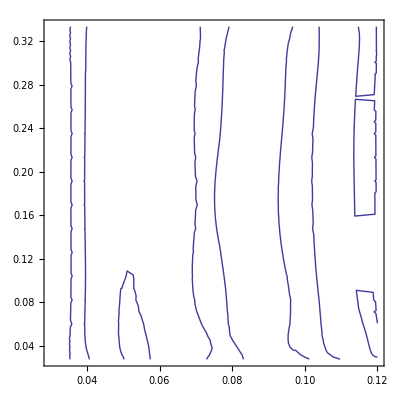

```mathematica
ContourPlot[{f22RelError[z,delta]== 10^-10, f22RelError[z,delta]== 10^-9}, {z, 3/100, 12/100}, {delta, 1/36, 1/3}]
```

f_27

### I1

```mathematica
f27I1Function[z_, delta_] := NIntegrate[Re[G[t] + t/2], {t, 0, (1 - delta)/z}]
f27I1Data =Re[Flatten[{#, Apply[f27I1Function, #]}] &/@ evaluationPoints];
```

```mathematica
f27I1Model = NonlinearModelFit[f27I1Data, polynomial,coefficients, {z, delta}] ;
f27I1Model["BestFitParameters"]
f27I1 = f27I1Model["Function"];
Max[f27I1Model["FitResiduals"]]
Max[f27I1Model["StandardizedResiduals"]]
```

{cc0000→57642.4,cc0010→76628.,cc0011→-81792.4,cc0020→102652.,cc0021→-222629.,cc0022→-199816.,cc0030→127143.,cc0031→-380273.,cc0032→128878.,cc0033→2.55615×10^6,cc0040→148738.,cc0041→-617860.,cc0042→130549.,cc0043→2.79611×10^6,cc0044→-1.29452×10^7,cc1000→-324330.,cc1010→-459651.,cc1011→563663.,cc1020→-602853.,cc1021→1.17157×10^6,cc1022→1.27711×10^6,cc1030→-745486.,cc1031→2.10862×10^6,cc1032→359437.,cc1033→-1.34257×10^7,cc1040→-882130.,cc1041→3.43579×10^6,cc1042→-1.76721×10^6,cc1043→-1.49114×10^7,cc1044→7.16109×10^7,cc1100→265633.,cc1110→375689.,cc1111→-353985.,cc1120→499904.,cc1121→-726808.,cc1122→-688271.,cc1130→630578.,cc1131→-1.30676×10^6,cc1132→-244248.,cc1133→7.60287×10^6,cc1140→761877.,cc1141→-2.14695×10^6,cc1142→707712.,cc1143→8.82087×10^6,cc1144→-4.14318×10^7,cc2000→1.01975×10^6,cc2010→1.43667×10^6,cc2011→-1.57181×10^6,cc2020→1.8949×10^6,cc2021→-3.27615×10^6,cc2022→-3.17741×10^6,cc2030→2.36511×10^6,cc2031→-5.88494×10^6,cc2032→-882989.,cc2033→3.63728×10^7,cc2040→2.82361×10^6,cc2041→-9.63322×10^6,cc2042→3.90824×10^6,cc2043→4.14259×10^7,cc2044→-1.95904×10^8,cc2100→235723.,cc2110→333218.,cc2111→-319771.,cc2120→442572.,cc2121→-669307.,cc2122→-650072.,cc2130→556918.,cc2131→-1.2019×10^6,cc2132→-187740.,cc2133→7.20321×10^6,cc2140→671450.,cc2141→-1.97327×10^6,cc2142→683322.,cc2143→8.04771×10^6,cc2144→-3.82695×10^7,cc2200→-10255.9,cc2210→-13176.8,cc2211→29330.8,cc2220→-16488.4,cc2221→53171.1,cc2222→18950.9,cc2230→-19482.8,cc2231→93900.,cc2232→15890.8,cc2233→-528062.,cc2240→-21595.2,cc2241→154478.,cc2242→-50985.,cc2243→-969788.,cc2244→3.99304×10^6,cc3000→-476549.,cc3010→-668979.,cc3011→789679.,cc3020→-879719.,cc3021→1.59614×10^6,cc3022→1.47036×10^6,cc3030→-1.09409×10^6,cc3031→2.86791×10^6,cc3032→487525.,cc3033→-1.74933×10^7,cc3040→-1.30163×10^6,cc3041→4.69713×10^6,cc3042→-1.92964×10^6,cc3043→-2.11588×10^7,cc3044→9.82863×10^7,cc3100→15875.4,cc3110→22914.,cc3111→3789.92,cc3120→31560.4,cc3121→-18237.5,cc3122→-41963.2,cc3130→41258.6,cc3131→-32077.8,cc3132→50831.5,cc3133→288865.,cc3140→51403.8,cc3141→-49865.9,cc3142→-33957.3,cc3143→-190545.,cc3144→246212.,cc3200→61603.5,cc3210→87768.8,cc3211→-88575.4,cc3220→116306.,cc3221→-183770.,cc3222→-193924.,cc3230→146025.,cc3231→-331357.,cc3232→-62736.5,cc3233→2.01029×10^6,cc3240→175469.,cc3241→-542891.,cc3242→228862.,cc3243→2.20708×10^6,cc3244→-1.06382×10^7,cc3300→13227.6,cc3310→18577.,cc3311→-24726.,cc3320→24203.6,cc3321→-50933.6,cc3322→-47877.7,cc3330→29786.3,cc3331→-91348.3,cc3332→-14878.5,cc3333→561817.,cc3340→34940.1,cc3341→-149220.,cc3342→71601.7,cc3343→705470.,cc3344→-3.24868×10^6,cc4000→667694.,cc4010→945688.,cc4011→-903389.,cc4020→1.25729×10^6,cc4021→-1.82679×10^6,cc4022→-1.74362×10^6,cc4030→1.58651×10^6,cc4031→-3.28983×10^6,cc4032→-725640.,cc4033→1.86872×10^7,cc4040→1.91666×10^6,cc4041→-5.41024×10^6,cc4042→1.88586×10^6,cc4043→2.25484×10^7,cc4044→-1.05113×10^8,cc4100→-39622.7,cc4110→-55034.6,cc4111→101925.,cc4120→-70481.4,cc4121→183472.,cc4122→186482.,cc4130→-84835.6,cc4131→332398.,cc4132→104024.,cc4133→-2.28695×10^6,cc4140→-97089.2,cc4141→543428.,cc4142→-344757.,cc4143→-2.56249×10^6,cc4144→1.23184×10^7,cc4200→46771.9,cc4210→66959.4,cc4211→-56902.7,cc4220→89671.4,cc4221→-109938.,cc4222→-95345.8,cc4230→114129.,cc4231→-197315.,cc4232→-66100.8,cc4233→982759.,cc4240→139178.,cc4241→-327565.,cc4242→90358.5,cc4243→1.34957×10^6,cc4244→-6.07402×10^6,cc4300→-3318.06,cc4310→-4177.94,cc4311→14292.7,cc4320→-4857.13,cc4321→27805.4,cc4322→20643.3,cc4330→-5166.22,cc4331→49542.7,cc4332→3337.61,cc4333→-328613.,cc4340→-4879.44,cc4341→80607.2,cc4342→-44933.7,cc4343→-476416.,cc4344→2.09015×10^6,cc4400→478.297,cc4410→591.266,cc4411→156.942,cc4420→794.617,cc4421→-1100.16,cc4422→330.09,cc4430→1015.54,cc4431→-1724.85,cc4432→3531.72,cc4433→12028.8,cc4440→1244.79,cc4441→-2762.15,cc4442→-3696.06,cc4443→10685.,cc4444→-43041.2}

2.48989×10^-6

0.461671

### I2

```mathematica
f27I2Function[z_, delta_] := NIntegrate[(1 - z * t) Re[G[t] + t/2], {t, (1 - delta)/z, 1/z}]
f27I2Data =Re[Flatten[{#, Apply[f27I2Function, #]}] &/@ evaluationPoints];
```

```mathematica
f27I2Model = NonlinearModelFit[f27I2Data, polynomial,coefficients, {z, delta}] ;
f27I2 = f27I2Model["Function"];
f27I2Model["BestFitParameters"]
Max[f27I2Model["FitResiduals"]]
Max[f27I2Model["StandardizedResiduals"]]
```

{cc0000→1084.03,cc0010→-3.09402,cc0011→-29662.3,cc0020→-1384.01,cc0021→-14585.2,cc0022→177179.,cc0030→-2230.7,cc0031→-14066.9,cc0032→45962.3,cc0033→-526830.,cc0040→-3269.83,cc0041→-17595.7,cc0042→78188.1,cc0043→-174619.,cc0044→1.09177×10^6,cc1000→-6191.4,cc1010→989.848,cc1011→127245.,cc1020→6684.98,cc1021→93400.1,cc1022→-751669.,cc1030→12188.2,cc1031→95706.2,cc1032→-490149.,cc1033→2.97638×10^6,cc1040→18402.9,cc1041→108370.,cc1042→-608774.,cc1043→1.70004×10^6,cc1044→-7.56612×10^6,cc1100→1903.62,cc1110→30.2982,cc1111→-60410.3,cc1120→-3113.81,cc1121→-71604.,cc1122→403579.,cc1130→-6768.81,cc1131→-71525.,cc1132→545822.,cc1133→-1.9301×10^6,cc1140→-10515.2,cc1141→-60221.,cc1142→698085.,cc1143→-2.67519×10^6,cc1144→7.73355×10^6,cc2000→11158.2,cc2010→-1473.21,cc2011→-280873.,cc2020→-15687.9,cc2021→-295303.,cc2022→1.6655×10^6,cc2030→-31885.1,cc2031→-312316.,cc2032→1.94786×10^6,cc2033→-8.05152×10^6,cc2040→-49503.8,cc2041→-311462.,cc2042→2.4722×10^6,cc2043→-8.50852×10^6,cc2044→2.80654×10^7,cc2100→2446.64,cc2110→-105.135,cc2111→-63119.4,cc2120→-3158.46,cc2121→-62728.5,cc2122→416256.,cc2130→-6448.21,cc2131→-60780.8,cc2132→452766.,cc2133→-2.01231×10^6,cc2140→-9851.25,cc2141→-52926.4,cc2142→575728.,cc2143→-1.90886×10^6,cc2144→6.23423×10^6,cc2200→935.038,cc2210→-60.1576,cc2211→-8633.24,cc2220→-106.286,cc2221→7204.96,cc2222→68769.2,cc2230→240.231,cc2231→12928.,cc2232→-54430.1,cc2233→-295590.,cc2240→679.757,cc2241→14602.6,cc2242→-75981.,cc2243→596293.,cc2244→-1.07244×10^6,cc3000→-1266.22,cc3010→358.887,cc3011→90692.5,cc3020→6329.89,cc3021→153357.,cc3022→-496540.,cc3030→14482.2,cc3031→179633.,cc3032→-1.03872×10^6,cc3033→2.48033×10^6,cc3040→23594.3,cc3041→184220.,cc3042→-1.33902×10^6,cc3043→5.67038×10^6,cc3044→-1.59219×10^7,cc3100→1596.14,cc3110→-110.671,cc3111→-20086.8,cc3120→-571.867,cc3121→1874.58,cc3122→141778.,cc3130→-534.57,cc3131→9437.62,cc3132→-20763.1,cc3133→-643838.,cc3140→-388.773,cc3141→12132.5,cc3142→-31667.8,cc3143→570342.,cc3144→-685960.,cc3200→1119.92,cc3210→-114.329,cc3211→-21073.,cc3220→-1021.51,cc3221→-15823.8,cc3222→128781.,cc3230→-1910.95,cc3231→-14630.2,cc3232→108023.,cc3233→-567750.,cc3240→-2839.27,cc3241→-13133.7,cc3242→133734.,cc3243→-401909.,cc3244→1.50794×10^6,cc3300→180.675,cc3310→-50.0902,cc3311→-3596.21,cc3320→-249.208,cc3321→-4341.3,cc3322→12847.9,cc3330→-508.52,cc3331→-5395.47,cc3332→27056.4,cc3333→-34026.2,cc3340→-806.43,cc3341→-5940.52,cc3342→34892.4,cc3343→-179930.,cc3344→484673.,cc4000→3508.17,cc4010→275.296,cc4011→-140761.,cc4020→-7425.34,cc4021→-182679.,cc4022→945492.,cc4030→-16694.3,cc4031→-188177.,cc4032→1.39564×10^6,cc4033→-3.91209×10^6,cc4040→-26282.1,cc4041→-159326.,cc4042→1.81498×10^6,cc4043→-7.7894×10^6,cc4044→2.10674×10^7,cc4100→949.742,cc4110→-22.8665,cc4111→532.709,cc4120→491.479,cc4121→19037.3,cc4122→-20060.9,cc4130→1445.,cc4131→25171.4,cc4132→-98926.5,cc4133→415467.,cc4140→2634.6,cc4141→31517.2,cc4142→-121565.,cc4143→250988.,cc4144→-1.13115×10^6,cc4200→367.678,cc4210→22.9334,cc4211→-7552.3,cc4220→-424.878,cc4221→-11914.4,cc4222→37083.1,cc4230→-1022.76,cc4231→-12478.2,cc4232→115021.,cc4233→-130617.,cc4240→-1606.77,cc4241→-8032.18,cc4242→144390.,cc4243→-779868.,cc4244→1.77159×10^6,cc4300→240.782,cc4310→10.4502,cc4311→-1392.13,cc4320→47.1639,cc4321→2733.02,cc4322→14915.8,cc4330→200.202,cc4331→4810.3,cc4332→-12293.,cc4333→-79010.3,cc4340→407.695,cc4341→6374.53,cc4342→-17915.7,cc4343→142051.,cc4344→-296656.,cc4400→30.2412,cc4410→-3.56744,cc4411→-298.66,cc4420→-11.7198,cc4421→-31.9645,cc4422→1265.74,cc4430→-15.7853,cc4431→29.7391,cc4432→357.389,cc4433→-5236.33,cc4440→-18.7533,cc4441→86.6731,cc4442→677.893,cc4443→-727.713,cc4444→6253.17}

1.95873×10^-7

0.556893

### relative error

```mathematica
f27[z_, delta_] := -8z^2/9(delta * f27I1Function[z, delta] + f27I2Function[z, delta])
f27Approx[z_, delta_] := -8z^2/9(delta * f27I1[z, delta] + f27I2[z, delta])
f27RelError[z_, delta_]:=Abs[(f27[z, delta] - f27Approx[z, delta])/f27[z, delta]]
```

```mathematica
f27RelError[0.19^2, 1/3]
f27RelError[0.19^2, 11/36]
f27RelError[0.19^2, 1/5]
f27RelError[0.29^2, 1/3]
f27RelError[0.29^2, 11/36]
f27RelError[0.29^2, 1/5]
```

8.77689×10^-8

7.29711×10^-8

4.61939×10^-8

8.70449×10^-8

2.66132×10^-7

1.03601×10^-6

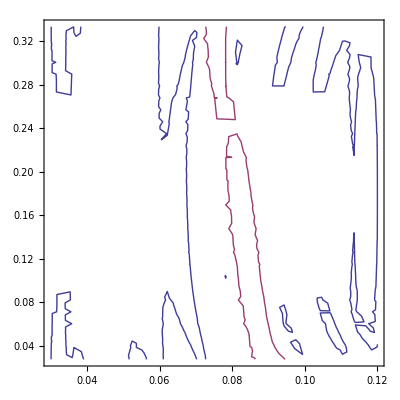

```mathematica
ContourPlot[{f27RelError[z,delta]== 10^-7, f27RelError[z,delta]== 10^-6}, {z, 3/100, 12/100}, {delta, 1/36, 1/3}]
```